```mathematica
R=60;
h=0.05;
```

```mathematica
bend[z_]:=-3I(z-h I)/(z-h I -R I)
unbend=InverseFunction[bend];
circleRadius[a_,b_,c_]:=Block[{p1,p2,p3,p},
p1=Abs[b-a];p2=Abs[c-b];p3=Abs[a-c];p=1/2(p1+p2+p3);
Return[(p1 p2 p3)/(4Sqrt[p(p-p1)(p-p2)(p-p3)])//FullSimplify]
]
circleCenter[a_,b_,c_]:=Block[{p1,p2,p3,p},
p1=Abs[b-a];p2=Abs[c-b];p3=Abs[a-c];p=1/2(p1+p2+p3);Return[ReIm[a-(Conjugate[c-b](b-a) (a-c))/(4 I Sqrt[p(p-p1)(p-p2)(p-p3)])]//FullSimplify];
];
circleFromPoints[a_,b_,c_]:=Circle[circleCenter[a,b,c],circleRadius[a,b,c]];
arcFromPoints[a_,b_,c_]:=Circle[
circleCenter[a,b,c],circleRadius[a,b,c],
{ArcTan@@(ReIm[c]-circleCenter[a,b,c]),
Mod[ArcTan@@(ReIm[a]-circleCenter[a,b,c]),2π]}
];
```

```mathematica
maxRadius=1.1circleRadius@@(bend@{-5,5I,5});
```

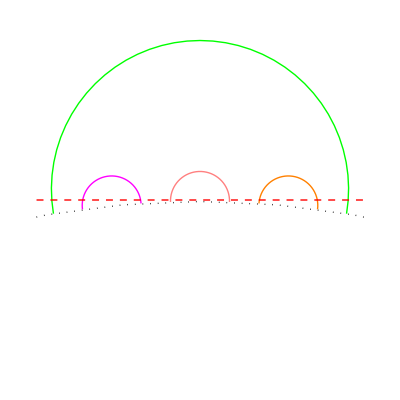

```mathematica
circleI=arcFromPoints@@(bend@{-1,I,1});
circleL=arcFromPoints@@(bend@{-4,-3+I,-2});
circleR=arcFromPoints@@(bend@{2,3+I,4});
circleO=arcFromPoints@@(bend@{-5,5I,5});
circleX=circleFromPoints@@(bend@{-1,0,1});
lineCutoff=Line[{{-maxRadius,0},{maxRadius,0}}];
background={
Pink,circleI,
Magenta,circleL,
Orange,circleR,
Green,circleO,
Black,Dotted,circleX,
Red,Dashed,lineCutoff};
Graphics[background,PlotRange->{{-maxRadius,maxRadius},{-maxRadius,maxRadius}}]
```

```mathematica
Tsolution=First[Solve[{(a(-4)+b)/(c(-4)+d)==4,(a(-3+h+I Sqrt[1-h^2])+b)/(c(-3+h+I Sqrt[1-h^2])+d)==(3+h+I Sqrt[1-h^2]),(a(-2)+b)/(c(-2)+d)==2},{a,b,c}]//Chop]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{a→1.0339 d,b→2.71186 d,c→0.338983 d}

```mathematica
Tsolution
```

{a→1.0339 d,b→2.71186 d,c→0.338983 d}

```mathematica
S[z_]:=5z;T[z_]:=Check[(a z+b)/(c z+d)/.Tsolution,ComplexInfinity];
Si=InverseFunction[S];Ti=InverseFunction[T];
```

```mathematica
HiddenIntervalMap[x_]=Which[
x<-5,Si,x>5,Si,
-4≤x≤-2,T,
-1≤x≤1,S,
2≤x≤4,Ti,
True,Identity];
```

```mathematica
ShootGeodesics[L1_,R1_]:=Module[{arcs,newArc,map},
arcs={{L1,R1}};
Do[
map=HiddenIntervalMap[arcs⟦-1,2⟧];
If[map==Identity,Break[]];
newArc={map[arcs⟦-1,1⟧],map[arcs⟦-1,2⟧]};
If[MemberQ[arcs,newArc],AppendTo[arcs,newArc];Break[]];
AppendTo[arcs,newArc];
,8];
Return[arcs];
]
```

```mathematica
ShowGeodesics[L1_,R1_]:=Module[{geodesics,geodesicplots},
geodesics=ShootGeodesics[L1,R1];
geodesicplots=Table[arcFromPoints@@(bend@{First[lr],Mean[lr]+I Abs[(lr⟦2⟧-lr⟦1⟧)/2],Last[lr]}),{lr,geodesics}];
geodesicplots=Join[{Dashing[None],Black},Riffle[Table[Opacity[1/i^2],{i,1,Length[geodesics]}],geodesicplots]];
Return[Graphics[Join[background,geodesicplots],PlotRange->{{-maxRadius,maxRadius},{-maxRadius,maxRadius}}]];
]
```

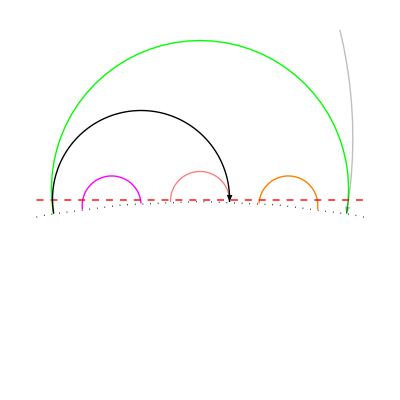

```mathematica
ShowGeodesics[-4.99,1]
```

```mathematica
manimate=Animate[Show[ShowGeodesics[-4.98,x]],{x,-4.985,4.995,0.01},AnimationRate->0.7]
```

```mathematica
Export[NotebookDirectory[]<>"geodesics.mov",manimate,ImageResolution->800,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"]
```

/Users/zfisher/Desktop/geodesics.mov

```mathematica
ShootGeodesics[-4.98,-2.95]
```

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

$Aborted[]